```mathematica
Clear["Global`*"];
```

```mathematica
Clear["Global`*"];
nc=1.001; ω=0.0227817;E0=0.05338;ξ=0.0;Ip=0.5;
p0z=-1.0137534;p0x=0.42901813;ts0=150.60866+40.860932I;
tp=2 Pi nc/ω;
AFz[t_]:=-E0/(ω √(1+ξ^2)) Sin[(ω t)/(2 nc)]^2 Sin[ω t ]
AFx[t_]:=-(E0 ξ)/(ω √(1+ξ^2)) Sin[(ω t-Pi/2)/(2 nc)]^2 Cos[ω t ]
EFz[t_]:=-D[(AFz[τ]), τ]/.τ->t
EFx[t_]:=-D[(AFx[τ]), τ]/.τ->t
alphaz[t_]:=∫_t0^t AFz[τ]ⅆτ
alphax[t_]:=∫_t0^t AFx[τ]ⅆτ

ts=τ/.FindRoot[(AFz[τ]+p0z)^2+(AFx[τ]+p0x)^2+2Ip==0,{τ, ts0}]
t0=Re[ts]
vz[t_]:=p0z+AFz[t]
vx[t_]:=p0x+AFx[t]
z[t_]:=alphaz[t]+p0z t-Re[alphaz[ts]]-Re[p0z ts]
x[t_]:=alphax[t]+p0x t-Re[alphax[ts]]-Re[p0x ts]
```

153.041+21.6333 ⅈ

153.041

```mathematica
Print["t_s0 = ",ts0, "      ","t_s = ",ts];
Print["E_z(t_s) = ",EFz[ts], "      ","E_x(t_s) = ",EFx[ts]];
Print["A_z(t_s) = ",AFz[ts], "      ","A_x(t_s) = ",AFx[ts]];
Print["E_z(t_0) = ",EFz[t0], "      ","E_x(t_0) = ",EFx[t0]];
Print["A_z(t_0) = ",AFz[t0], "      ","A_x(t_0) = ",AFx[t0]];
Print["α_z(t_s) = ",alphaz[ts], "      ", "α_x(t_s) = ",alphax[ts]];
Print["z(t_s) = ",z[ts], "      ","x(t_s) = ",x[ts]];
Print["z(t_0) = ",z[t0], "      ","x(t_0) = ",x[t0]];
Print["vz(t_s) = ",vz[ts], "      ","vx(t_s) = ",vx[ts]];
Print["vz(t_0) = ",vz[t0], "      ","vx(t_0) = ",vx[t0]];
```

t_s0 = 150.609+40.8609 ⅈ      t_s = 153.041+21.6333 ⅈ

E_z(t_s) = -0.05973+0.0241149 ⅈ      E_x(t_s) = 0

A_z(t_s) = 1.01375+1.08814 ⅈ      A_x(t_s) = 0.+0. ⅈ

E_z(t_0) = -0.0457663      E_x(t_0) = 0

A_z(t_0) = 0.76944      A_x(t_0) = 0.

α_z(t_s) = -11.2327+18.3605 ⅈ      α_x(t_s) = 0.

z(t_s) = 0.-3.57039 ⅈ      x(t_s) = 0.+9.28109 ⅈ

z(t_0) = 11.2327      x(t_0) = 0.

vz(t_s) = 1.11022×10^-15+1.08814 ⅈ      vx(t_s) = 0.429018+0. ⅈ

vz(t_0) = -0.244313      vx(t_0) = 0.429018

{{xx→InterpolatingFunction[{{202.332,826.735}},<>],zz→InterpolatingFunction[{{202.332,826.735}},<>]}}

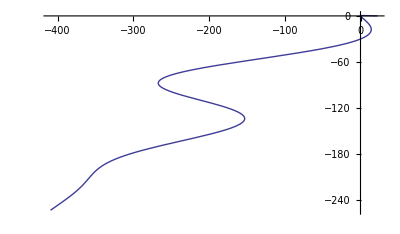

{{-252.945,-409.323}}

```mathematica
s=NDSolve[{xx''[t]==-EFx[t]-xx[t]/(xx[t]^2+zz[t]^2)^(3/2),zz''[t]==-EFz[t]-zz[t]/(xx[t]^2+zz[t]^2)^(3/2),xx[t0]==x[t0],zz[t0]==z[t0],xx'[t0]==vx[t0],zz'[t0]==vz[t0]},{xx,zz},{t,t0,tp}]
ParametricPlot[Evaluate[{zz[t],xx[t]}/.s],{t,t0,tp}]
{xx[tp], zz[tp]}/.s
```